# Phase Transition with Extra Scalar at 10^5 GeV

```mathematica
ClearAll["Global`*"]
```

## Threshold correction

```mathematica
Vtree=-1/2 μHL^2 hL^2-1/2 μHR^2 hR^2+1/4 λR (hL^4+hR^4)-1/2 A S(hL^2+hR^2-vR^2-vL^2)+1/4 λLR hL^2 hR^2+1/2 μS^2 S^2;
```

```mathematica
$Assumptions={{μHL,μHR,λR,λLR,A,vR,vL,μS}∈PositiveReals,{hL,hR,S}∈Reals};
D[Vtree,hR]
sol=(Solve[D[Vtree,hR]==0,hR]//Normal)[[2]];
hR^2/.sol//Simplify
```

-A hR S+1/2 hL^2 hR λLR+hR^3 λR-hR μHR^2

(2 A S-hL^2 λLR+2 μHR^2)/(2 λR)

```mathematica
VEW=Vtree/.sol//FullSimplify
```

1/(16 λR)(-4 A^2 S^2-hL^4 (λLR^2-4 λR^2)-4 μHR^4+4 A S (hL^2 (λLR-2 λR)+2 (vL^2+vR^2) λR-2 μHR^2)+hL^2 (-8 λR μHL^2+4 λLR μHR^2)+8 S^2 λR μS^2)

```mathematica
Coefficient[VEW,hL,4]/(λR/4)//Simplify
```

1-λLR^2/(4 λR^2)

λ_L=λ_R(1-λ_LR/(4 λ_R^2))

```mathematica
NSolve[0.05==λR(1-0.01^2/(4 λR^2)),λR,PositiveReals][[1]]
```

{λR→0.0504951}

```mathematica
Coefficient[VEW,S hL^2]//Simplify
```

(A (-2 λ+λLR))/(4 λ)

A_EW=A_high(1-λ_LR/(2 λ_R))

```mathematica
Coefficient[VEW,S,2]*2//Simplify
```

-A^2/(2 λ)+μS^2

(μS^2)_EW=(μS^2)_high-A_high^2/(2 λ_R)

### S_R+S_L model

```mathematica
Vtree=-1/2 μHL^2 hL^2-1/2 μHR^2 hR^2+1/4 λR (hL^4+hR^4)-1/2 A SL(hL^2-vL^2)-1/2 A SR(hR^2-vR^2)+1/4 λLR hL^2 hR^2+1/2 μS^2(SL^2+SR^2);
```

```mathematica
$Assumptions={{μHL,μHR,λR,λLR,A,vR,vL,μS}∈PositiveReals,{hL,hR,SL,SR}∈Reals};
D[Vtree,hR]
sol=(Solve[D[Vtree,hR]==0,hR]//Normal)[[-1]];
hR^2/.sol//Simplify
```

-A hR SR+1/2 hL^2 hR λLR+hR^3 λR-hR μHR^2

(2 A SR-hL^2 λLR+2 μHR^2)/(2 λR)

```mathematica
VEW=Vtree/.sol//FullSimplify
```

1/(16 λR)(-4 A^2 SR^2+4 A hL^2 (SR λLR-2 SL λR)-hL^4 (λLR^2-4 λR^2)-4 μHR^4+8 A (SL vL^2 λR+SR vR^2 λR-SR μHR^2)+hL^2 (-8 λR μHL^2+4 λLR μHR^2)+8 (SL^2+SR^2) λR μS^2)

```mathematica
Coefficient[VEW,hL,4]/(λR/4)//Simplify
```

1-λLR^2/(4 λR^2)

```mathematica
Coefficient[VEW,SL hL^2]//Simplify
```

-A/2

```mathematica
Coefficient[VEW,SR hL^2]//Simplify
```

(A λLR)/(4 λR)

```mathematica
Coefficient[VEW,SL,2]
```

μS^2/2

```mathematica
Coefficient[VEW,SR,2]//Simplify
```

-(A^2-2 λR μS^2)/(4 λR)

## Running parameters

### SM Parameters

```mathematica
ClearAll["Global`*"]
sw = √0.23116;
cw = √(1 - sw^2);
mZ = 91.1876; 
mW = 80.399;
(*mtpole = 173.1-0.7*2.5;*)
GF = 1.16637 10^-5;
v=1/(√(√2*GF));
mb=4.19;mc=1.27;ms=0.1;
α0=1/137.035999679;
ΔαhmZ=0.02758;
αmZ= α0/(1-0.03150-ΔαhmZ+0.00007);
αsmZ=0.1181+0.0011*(1);

Mpl=2.4*10^18;(*Planck mass*)
mhpole=125.18+0.16*(0);

ye=2.8*10^-6;
yμ=5.9*10^-4;
yτ=1.0*10^-2;
yd=1.6*10^-5/2;
ys=3.1*10^-4/2;
yb=1.6*10^-2/2;
yu=7.4*10^-6/2;
yc=3.6*10^-3/2;
```

### Running equations

```mathematica
(*Phase space factor*)
κ=1/(16*Pi^2); 

(*numbers of flavors*)
nf=6;
ng=3;
z3=Zeta[3];

(*QCD colour factors*)
ca=3;
dR=3;
cf=4/3;
cr=1/2;

(*Beta function for top-Yukawa*)βyt[λ_,yt_,g3_,g2_,g1_]:=2*yt*(+κ*yt^2*(3/4+1/2*dR)+κ*g3^2*(-3*cf)+κ^2*λ^2*(3)+κ^2*yt^2*λ*(-6)+κ^2*yt^4*(3/4-9/4*dR)+κ^2*g3^2*yt^2*(6*cf+5/2*cf*dR)+κ^2*g3^4*(-3/2*cf^2-97/6*ca*cf+10/3*nf*cr*cf)+κ^3*λ^3*(-18)+κ^3*yt^2*λ^2*(285/8-45/4*dR)+κ^3*yt^4*λ*(63/2+45/2*dR)+κ^3*yt^6*(-345/32+107/32*dR+39/16*dR^2+9/4*z3+3/2*z3*dR)+κ^3*g3^2*yt^2*λ*(6*cf)+κ^3*g3^2*yt^4*(-57/2*cf-81/8*cf*dR)+κ^3*g3^4*yt^2*(471/16*cf^2-119/8*cf^2*dR+25*cr*cf+717/16*ca*cf+77/4*ca*cf*dR-33/4*nf*cr*cf-4*nf*cr*cf*dR-27*z3*cf^2+18*z3*cf^2*dR-27/2*z3*ca*cf-9*z3*ca*cf*dR)+κ^3*g3^6*(-129/2*cf^3+129/4*ca*cf^2-11413/108*ca^2*cf+46*nf*cr*cf^2+556/27*nf*ca*cr*cf+140/27*nf^2*cr^2*cf-48*z3*nf*cr*cf^2+48*z3*nf*ca*cr*cf))+yt κ(-9/4 g2^2-17/12 g1^2)+yt κ^2(5/2 yt^2(17/12 g1^2+9/4 g2^2)+yt^2(223/48 g1^2+135/16 g2^2)+25/9 g1^4(9/200+29/45*ng)-3/4 g1^2 g2^2+19/9 g1^2 g3^2-(35/4-ng)g2^4+9 g2^2 g3^2);

(*Beta function for the gauge couplings*)
βg3[λ_,yt_,g3_,g2_,g1_]:=2*g3*(+κ*g3^2*(-11/6*ca+2/3*nf*cr)+κ^2*g3^2*yt^2*(-2*cr)+κ^2*g3^4*(-17/3*ca^2+2*nf*cr*cf+10/3*nf*ca*cr)+κ^3*g3^2*yt^4*(9/2*cr+7/2*cr*dR)+κ^3*g3^4*yt^2*(-3*cr*cf-12*ca*cr)+κ^3*g3^6*(-2857/108*ca^3-nf*cr*cf^2+205/18*nf*ca*cr*cf+1415/54*nf*ca^2*cr-22/9*nf^2*cr^2*cf-79/27*nf^2*ca*cr^2))+g3^3 κ^2(11/6 g1^2+9/2 g2^2);
βg1[λ_,yt_,g3_,g2_,g1_]:=-g1^3 κ(-1/6-20/9*ng)+g1^3 κ^2 5/3(199/30 g1^2+27/10 g2^2+44/5 g3^2-17/10 yt^2);
βg2[λ_,yt_,g3_,g2_,g1_]:=-g2^3 κ(43/6-4/3*ng)+g2^3 κ^2(3/2 g1^2+35/6 g2^2+12 g3^2-3/2 yt^2);

(*Beta function for the quartic self-coupling of the scalar field*)
βλ[λ_,yt_,g3_,g2_,g1_]:=2*(+κ*λ^2*(12)+κ*yt^2*λ*(2*dR)+κ*yt^4*(-dR)+κ^2*λ^3*(-156)+κ^2*yt^2*λ^2*(-24*dR)+κ^2*yt^4*λ*(-1/2*dR)+κ^2*yt^6*(5*dR)+κ^2*g3^2*yt^2*λ*(10*cf*dR)+κ^2*g3^2*yt^4*(-4*cf*dR)+κ^3*λ^4*(3588+2016*z3)+κ^3*yt^2*λ^3*(291*dR)+κ^3*yt^4*λ^2*(789/2*dR-36*dR^2+252*z3*dR)+κ^3*yt^6*λ*(-1881/8*dR+80*dR^2-66*z3*dR)+κ^3*yt^8*(13/2*dR-195/8*dR^2-12*z3*dR)+κ^3*g3^2*yt^2*λ^2*(-306*cf*dR+288*z3*cf*dR)+κ^3*g3^2*yt^4*λ*(895/4*cf*dR-324*z3*cf*dR)+κ^3*g3^2*yt^6*(-19/2*cf*dR+60*z3*cf*dR)+κ^3*g3^4*yt^2*λ*(-119/2*cf^2*dR+77*ca*cf*dR-16*nf*cr*cf*dR+72*z3*cf^2*dR-36*z3*ca*cf*dR)+κ^3*g3^4*yt^4*(131/2*cf^2*dR+48*cr*cf*dR-109/2*ca*cf*dR+10*nf*cr*cf*dR-48*z3*cf^2*dR+24*z3*ca*cf*dR))+κ/2(-(3 g1^2+9 g2^2)2λ+9/4(1/3 g1^4+2/3 g1^2 g2^2+g2^4))+κ^2/2((54 g2^2+18 g1^2)4 λ^2-((313/8-10ng)g2^4-39/4 g2^2 g1^2-(687/200+2ng)25/9 g1^4)2λ+(497/8-8ng)g2^6-(97/40+8/5 ng)5/3 g2^4 g1^2-(717/200+8/5 ng)25/9 g2^2 g1^4-(531/1000+24/25 ng)125/27 g1^6-8/3 g1^2 2 yt^4-9/2 g2^4 yt^2+5/3 g1^2(63/5 g2^2-57/10 g1^2)yt^2+10*2 λ yt^2(17/12 g1^2+9/4 g2^2));
βA[λ_,yt_,g3_,g2_,g1_,A_]=2κ A(6 λ+3 yt^2+3 yb^2+yτ^2-9/4 g2^2-9/20 g1^2);
(*measured gauge coupling*)
g1mZ=(√(4π αmZ))/cw;
g2mZ=(√(4π αmZ))/sw;
g3mZ=√(4π*αsmZ);
αsmZ=0.1179;

(*Measured pole masses*)
mhpole=125.10;
mtpole=172.76;

(*MSbar couplings*)
λmtpole:=0.12604+0.00206*(mhpole-125.15)-0.00004(mtpole-173.34);
ytmtpole:=0.93690+0.00556(mtpole-173.34)-0.00003(mhpole-125.15)-0.00042((αsmZ-0.1184)/0.0007);
g3mtpole=1.1666+0.00314((αsmZ-0.1184)/0.0007)-0.00046(mtpole-173.34);
g2mtpole=0.64779+0.00004(mtpole-173.34)+0.00011*(mW-80.384)/0.014;
g1mtpole=0.35830+0.00011(mtpole-173.34)-0.00020*(mW-80.384)/0.014;
(*IW: should these equations be updated? These equations come from the near criticality paper, but that paper cites a measured value different from the current value*)
```

## Parametrization at T=0

```mathematica
μS2[mS_,sinθ_]:=sinθ^2 mhpole^2+(1-sinθ^2)mS^2;
A[mS_,sinθ_]:=((mhpole^2-mS^2)sinθ √(1-sinθ^2))/v;
λhL[mS_,sinθ_]:=((1-sinθ^2)mhpole^2+sinθ^2 mS^2)/(2 v^2);
```

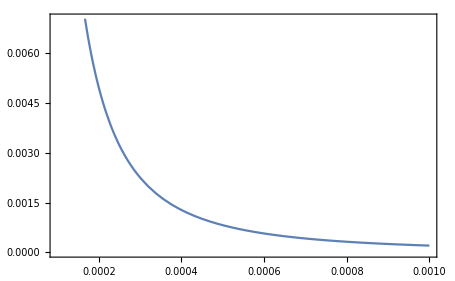

```mathematica
Plot[λhL[0.005,sin]-A[0.005,sin]^2/(2μS2[0.005,sin]),{sin,10^-4,10^-3}]
```

```mathematica
((1-sinθ^2)mh^2+sinθ^2 mS^2)/(2 vE^2)-((mh^2-mS^2)^2 sinθ^2(1-sinθ^2))/(2 vE^2)1/(sinθ^2 mh^2+(1-sinθ^2)mS^2)//Simplify
```

-(mh^2 mS^2)/(2 (-mh^2 sinθ^2+mS^2 (-1+sinθ^2)) vE^2)

```mathematica
mS^2/(sinθ^2 mh^2+(1-sinθ^2)mS^2)//Simplify
```

mS^2/(mS^2+mh^2 sinθ^2-mS^2 sinθ^2)

## Find Phase transition strength

```mathematica
vR=20000;
aB=Exp[3.91];
aF=Exp[1.14];
```

```mathematica
transition‵strength[mS_,sinθ_]:=(
λbound=λhL[mS,sinθ];
Abound=A[mS,sinθ];
μS=√μS2[mS,sinθ];
s:=NDSolve[{hλ'[t]==βλ[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hyt'[t]==βyt[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg3'[t]==βg3[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg2'[t]==βg2[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hg1'[t]==βg1[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t]],hA'[t]==βA[hλ[t],hyt[t],hg3[t],hg2[t],hg1[t],hA[t]],hA[Log[mtpole/mZ]]==Abound,hλ[Log[mtpole/mZ]]==λbound,hyt[Log[mtpole/mZ]]==ytmtpole,hg3[Log[mtpole/mZ]]==g3mtpole,hg2[Log[mtpole/mZ]]==g2mtpole,hg1[Log[mtpole/mZ]]==g1mtpole},{hg1,hg2,hg3,hλ,hyt,hA},{t,-6,17*Log[10]},MaxSteps->10^5];
{{g1[μ_]},{g2[μ_]},{g3[μ_]},{λ[μ_]},{yt[μ_]},{Afun[μ_]}}={hg1[Log[μ/mZ]]/.s,hg2[Log[μ/mZ]]/.s,hg3[Log[μ/mZ]]/.s,hλ[Log[μ/mZ]]/.s,hyt[Log[μ/mZ]]/.s,hA[Log[μ/mZ]]/.s};
g=g2[vR];
gY=g1[vR];
Avalue=Afun[vR];
λR=λ[vR];
ytR=yt[vR];
mWR=1/4 g^2 vR^2;
mZR=1/4(g^2+gY^2)vR^2;
mtR=1/2 ytR^2 vR^2;
DD=1/16(3 g^2+gY^2+4 ytR^2);
BB=3/(64 π^2 vR^4)(2 mWR^2+mZR^2-4 mtR^2);
EE=1/(32π)(2 g^3+(g^2+gY^2)^(3/2));
cs=2/3;
μH2=λR vR^2;

Deff=DD-(cs Avalue^2)/(4 μS^2);
λeff=λR-Avalue^2/(2 μS^2);
T0=√(1/(2Deff)(μH2-4 BB vR^2-(vR^2 Avalue^2)/(2 μS^2)));
mgauge=({{g^2 x1^2/4+11/6 g^2 x2^2, -g gY x1^2/4}, {-g gY x1^2/4, gY^2 x1^2/4+11/3 gY^2 x2^2}});
gaugeL=Eigenvalues[mgauge]//FullSimplify;
mWL[ϕ_,T_]:=1/4 g^2 ϕ^2+11/6 g^2 T^2;(*longitudal mode for W+ and W-, or W1 and W2*)
mBL[ϕ_,T_]:=gaugeL[[1]]/.{x1->ϕ,x2->T};(*SM B particle, massless*)
mZL[ϕ_,T_]:=gaugeL[[2]]/.{x1->ϕ,x2->T};(*Zprime particle*)
λT[T_]:=λeff-3/(16 π^2 vR^4)(2 mWR^2 Log[mWR/(aB T^2)]+mZR^2 Log[mZR/(aB T^2)]-4 mtR^2 Log[mtR/(aF T^2)]);
resum[ϕ_,T_]:=T/(12π)(2((mWR ϕ^2/vR^2)^(3/2)-mWL[ϕ,T]^(3/2))+((mZR ϕ^2/vR^2)^(3/2)-(mZL[ϕ,T])^(3/2))-Abs[mBL[ϕ,T]]^(3/2));
VhighT[ϕ_,T_]:=Deff (T^2-T0^2)ϕ^2-EE T ϕ^3+λT[T]/4 ϕ^4+resum[ϕ,T]-resum[10^-10,T];
T1=Catch[Do[If[FindMinimum[VhighT[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T0,1.2T0,0.1T0}]];
T2=Catch[Do[If[FindMinimum[VhighT[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T1-0.1T0,T1,0.01T0}]];
T3=Catch[Do[If[FindMinimum[VhighT[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T2-0.01T0,T2,0.001T0}]];
T4=Catch[Do[If[FindMinimum[VhighT[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T3-0.001T0,T3,0.0001T0}]];
Tc=Catch[Do[If[FindMinimum[VhighT[ϕ,T],{ϕ,vR}][[1]]>=0,Throw[T]],{T,T4-0.0001T0,T4,0.00001T0}]];
vev=ϕ/.FindMinimum[VhighT[ϕ,Tc],{ϕ,vR}][[2]];
strength=vev/Tc
)
```

```mathematica
λR
```

0.0658244[20000][20000][20000][20000][20000][20000]

```mathematica
ytR
```

0.753687

```mathematica
transition‵strength[10,0.066]
λeff
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

1.02161

0.00210918

```mathematica
Avalue
```

4.60206

```mathematica
μS
```

12.9513

```mathematica
0.066/10
```

0.0066

```mathematica
transition‵strength[40,0.275]
λeff
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

1.00135

0.00254597

```mathematica
0.28/40
```

0.007

```mathematica
λeff/λR
```

0.0466969

## Scan and plot

```mathematica
GeVlist=Table[{mS,sinθ=ratio*mS,transition‵strength[mS,sinθ],λeff},{mS,0.1,70,2},{ratio,0.006,0.008,0.0001}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

FindMinimum::nrnum: The function value 8.07702×10^14+6.36444×10^14 ⅈ is not a real number at {ϕ} = {20000.}.

FindMinimum::nrnum: The function value 7.58193×10^14+6.31736×10^14 ⅈ is not a real number at {ϕ} = {20000.}.

FindMinimum::nrnum: The function value 7.11535×10^14+6.2704×10^14 ⅈ is not a real number at {ϕ} = {20000.}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,20000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

```mathematica
GeVlist1=Flatten[GeVlist,1];
Export[NotebookDirectory[]<>"GeV-SFOPTbound-20TeV.csv",GeVlist1]
```

/Users/isaac/Dropbox/Research_Project/2021-9-Local_EWBG_parity/02-Analysis/Scalar-Ext/GeV-SFOPTbound-20TeV.csv

```mathematica
transition‵strength[0.005,0.000034]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

1.0534

```mathematica
0.000034/0.005
```

0.0068

```mathematica
0.000028/0.005
```

0.0056

```mathematica
MeVlist=Table[
{mS,sinθ=ratio*mS,transition‵strength[mS,sinθ],λeff},
{mS,0.001,1,0.005},{ratio,0.006,0.008,0.0001}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMinimum::nrnum: The function value 8.07691×10^14+6.36443×10^14 ⅈ is not a real number at {ϕ} = {20000.}.

FindMinimum::nrnum: The function value 7.58181×10^14+6.31735×10^14 ⅈ is not a real number at {ϕ} = {20000.}.

FindMinimum::nrnum: The function value 7.11522×10^14+6.27038×10^14 ⅈ is not a real number at {ϕ} = {20000.}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {ϕ,20000} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMinimum::sdprec will be suppressed during this calculation.

```mathematica
MeVlist1=Flatten[MeVlist,1];
Export[NotebookDirectory[]<>"MeV-SFOPTbound-20TeV.csv",MeVlist1]
```

/Users/isaac/Dropbox/Research_Project/2021-9-Local_EWBG_parity/02-Analysis/Scalar-Ext/MeV-SFOPTbound-20TeV.csv

```mathematica
transition‵strength[0.005,0.000026]
λeff
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

1.11021

0.0038701